```mathematica
(*sbc fit*)
(*(1-d)-(a^2*Sin[π*c*Sqrt[(x-b)^2+a^2]]^2)/((x-b)^2+a^2)*)
```

## Values

```mathematica
ftwToFrequencyMHz=(1.*^-6)*(1.*^9)/(Interpreter["HexInteger"]["FFFFFFFF"]);
mhz=1.*^6;
khz=1.*^3;
```

## Import

```mathematica
datasetName="C:\\Users\\EGGS2\\Documents\\tmp1\\000025582-Rabi Flopping.h5";
```

### Import

```mathematica
(*import dataset*)
res00=Import[datasetName,{"/datasets/results"}];
```

## Process

### Convert

```mathematica
(*rearrange for columns: secular (kHz), readout, carrier, counts*)
res01=Transpose[{
res00[[;;,4]]*1.*^-3,(*sideband, kHz*)
res00[[;;,1]]*ftwToFrequencyMHz,(*readout/AOM, MHz*)
res00[[;;,3]]*1.*^-6,(*carrier, MHz*)
res00[[;;,2]](*counts*)
}];
(*sample data*)
res01[[1]]
```

```mathematica
(*guess carrier frequency*)
carrierFreqMHz=Mean[res01[[;;,2]]];
(*find count threshold*)
countThreshold=FindThreshold[res01[[;;,-1]]];
```

```mathematica
(*create copy of dataset and directly threshold counts into states*)
res10=res01;
res10[[;;,-1]]=UnitStep[res01[[;;,-1]]-countThreshold];
(*average states into probabilities*)
res11=GroupBy[
res10,
#[[;;3]]&,
N[Mean[#]]&
]//Values;
```

### Rearrange

```mathematica
(*group first by secular frequency*)
res20=GroupBy[
res11,
First->Rest
];
```

```mathematica
(*separate into rsb and bsb*)
res21=GatherBy[
#,
First[#]<carrierFreqMHz&
]&/@res20;
(*sort frequencies by order*)
(*final output
key: eggs secular (kHz)
value: {bsb/rsb, readout/AOM freq (MHz), carrier freq (MHz), probability}*)
res21=Map[
SortBy[#,First]&,
res21,
{2}
];
(*sample dimensions*)
res21//Keys
res21//Values//Dimensions
```

{1199.5,1201.,1200.,1200.5,1199.}

{5,2,205,3}

### Plot

```mathematica
resPlots=KeyValueMap[
{ListDensityPlot[
#2[[2]],
PlotRange->Full,
PlotLegends->Automatic,
ColorFunctionScaling->False,
FrameLabel->{ 
{Style["EGGS Carrier (MHz)",{Black,Directive[15]}],None},
{Style["Readout Frequency (MHz)",{Black,Directive[15]}],
Style["EGGS ω_Sideband - "<>ToString[#1]<>" kHz\nRSB",{Black,Directive[15]}]}
},
ImageSize->Medium
],
ListDensityPlot[
#2[[1]],
PlotRange->Full,
PlotLegends->Automatic,
ColorFunctionScaling->False,
FrameLabel->{ 
{Style["EGGS Carrier (MHz)",{Black,Directive[15]}],None},
{Style["Readout Frequency (MHz)",{Black,Directive[15]}],
Style["EGGS ω_Sideband - "<>ToString[#1]<>" kHz\nBSB",{Black,Directive[15]}]}
},
ImageSize->Medium
]}&,
res21
];
```

```mathematica
(*ListPlot3D[
res21[[1,1]],
PlotRange->Full,
PlotLegends->Automatic,
PlotRange->Full
],*)
```

## Show

### Single Point

```mathematica
(*ListPlot[
#,
Joined->False,
PlotRange->{0,1}
]&/@res21[[1,;;,;;,{1,3}]]*)
```

### Full Scan

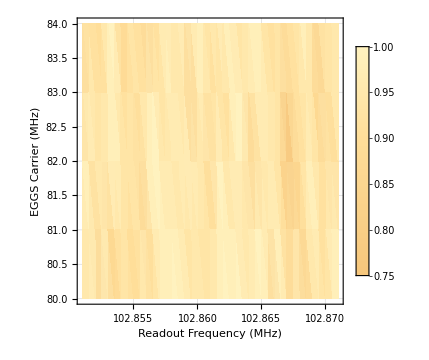
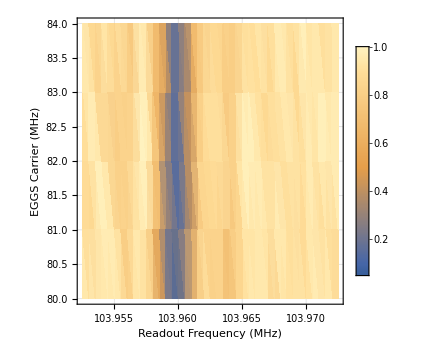
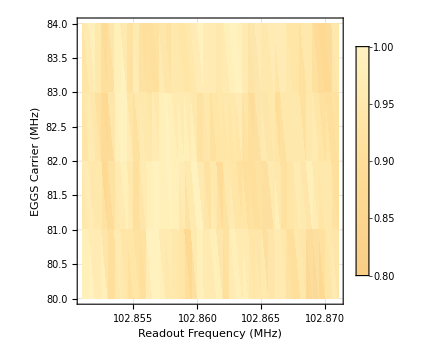
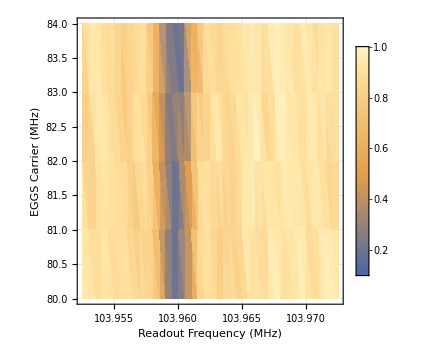
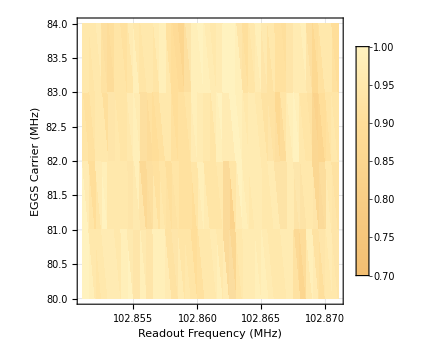
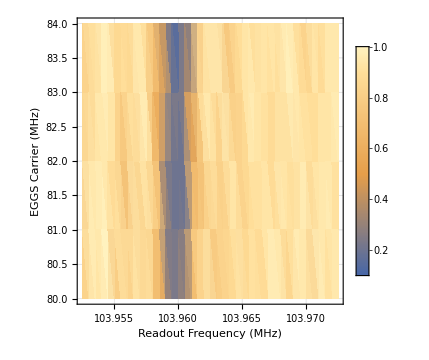

```mathematica
resPlots[[;;;;2]]
```